# Algorytm

## Wczytanie danych dla PD

```mathematica
allFilesPD04n2000 =FileNames["PD_4_2000*.csv","./data"]
```

{./data/PD_4_2000___01.csv,./data/PD_4_2000___02.csv,./data/PD_4_2000___03.csv,./data/PD_4_2000___04.csv,./data/PD_4_2000___05.csv,./data/PD_4_2000___06.csv,./data/PD_4_2000___07.csv,./data/PD_4_2000___08.csv,./data/PD_4_2000___09.csv,./data/PD_4_2000___10.csv,./data/PD_4_2000___11.csv,./data/PD_4_2000___12.csv,./data/PD_4_2000___13.csv,./data/PD_4_2000___14.csv,./data/PD_4_2000___15.csv,./data/PD_4_2000___16.csv,./data/PD_4_2000___17.csv,./data/PD_4_2000___18.csv,./data/PD_4_2000___19.csv,./data/PD_4_2000___20.csv}

```mathematica
allFilesPD08n1000 =FileNames["PD_8_2000*.csv","./data"]
```

{./data/PD_8_2000___01.csv,./data/PD_8_2000___02.csv,./data/PD_8_2000___03.csv,./data/PD_8_2000___04.csv,./data/PD_8_2000___05.csv,./data/PD_8_2000___06.csv,./data/PD_8_2000___07.csv,./data/PD_8_2000___08.csv,./data/PD_8_2000___09.csv,./data/PD_8_2000___10.csv,./data/PD_8_2000___11.csv,./data/PD_8_2000___12.csv,./data/PD_8_2000___13.csv,./data/PD_8_2000___14.csv,./data/PD_8_2000___15.csv,./data/PD_8_2000___16.csv,./data/PD_8_2000___17.csv,./data/PD_8_2000___18.csv,./data/PD_8_2000___19.csv,./data/PD_8_2000___20.csv}

```mathematica
allFilesPD16n1000 =FileNames["PD_16_2000*.csv","./data"]
```

{./data/PD_16_2000___01.csv,./data/PD_16_2000___02.csv,./data/PD_16_2000___03.csv,./data/PD_16_2000___04.csv,./data/PD_16_2000___05.csv,./data/PD_16_2000___06.csv,./data/PD_16_2000___07.csv,./data/PD_16_2000___08.csv,./data/PD_16_2000___09.csv,./data/PD_16_2000___10.csv,./data/PD_16_2000___11.csv,./data/PD_16_2000___12.csv,./data/PD_16_2000___13.csv,./data/PD_16_2000___14.csv,./data/PD_16_2000___15.csv,./data/PD_16_2000___16.csv,./data/PD_16_2000___17.csv,./data/PD_16_2000___18.csv,./data/PD_16_2000___19.csv,./data/PD_16_2000___20.csv}

## Proste wykresy

```mathematica
makePlot[s_]:=ListLinePlot[Rest@Import[s],PlotRange->{0,1},PlotLabel->s]
```

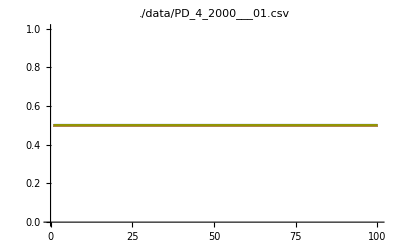
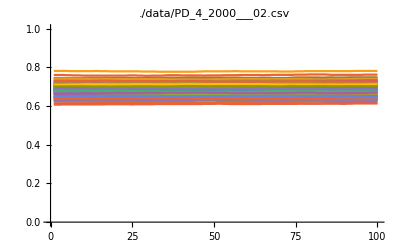
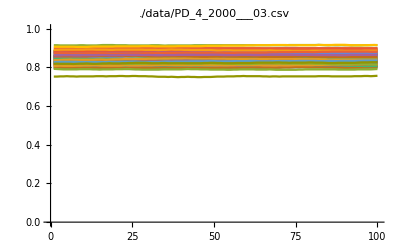
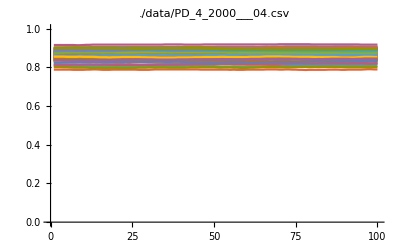
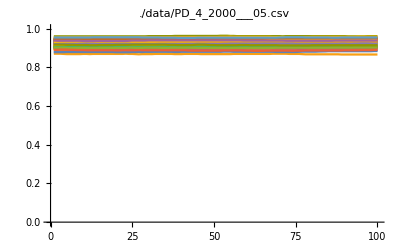
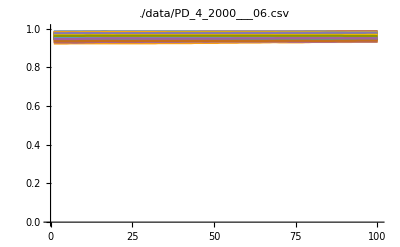
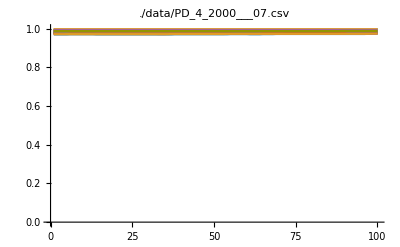
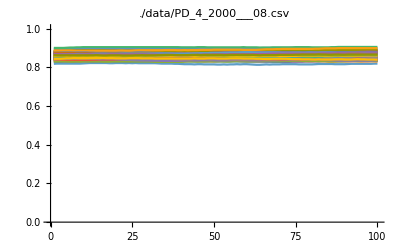

```mathematica
makePlot/@allFilesPD04n1000
```

## Testowanie czy liczba kroków coś zmienia

```mathematica
makeMean[s_]:=Mean[Flatten@Rest@Import[s]]
```

```mathematica
updateMakeMean[v_]:=Transpose[{Range[1,1.95,0.05],makeMean/@v}]
```

```mathematica
fig1=ListLinePlot[updateMakeMean[allFilesPD04n1000],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Blue];
```

```mathematica
fig2=ListLinePlot[updateMakeMean[allFilesPD04n2000],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Orange];
```

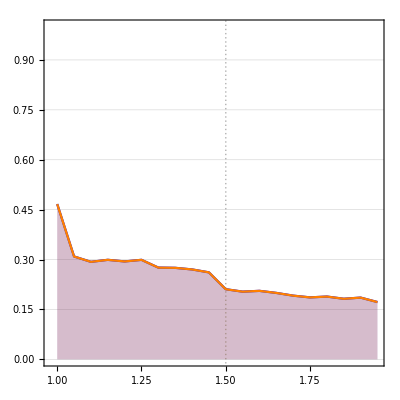

```mathematica
Show[fig1, fig2]
```

## Sprawdzanie profile dla różnych grafów

```mathematica
makeMean[s_]:=Mean[Flatten@Rest@Import[s]]
```

```mathematica
updateMakeMean[v_]:=Transpose[{Range[1,1.95,0.05],makeMean/@v}]
```

```mathematica
fig1=ListLinePlot[Callout[updateMakeMean[allFilesPD04n1000],"4"],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Blue];
```

```mathematica
fig2=ListLinePlot[Callout[updateMakeMean[allFilesPD08n1000],8],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Orange];
```

```mathematica
fig3=ListLinePlot[Callout[updateMakeMean[allFilesPD16n1000],16],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Cyan];
```

```mathematica
Show[fig1, fig2,fig3]
```

-Graphics-

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```